```mathematica
v[x_,q_]:=(√(1-q))/(π √(1-(1-q)x^2/4))∏_(k=0)^50 ((1-q^(2k+2))/(1-q^(2k+1))(1-(x^2(1-q)q^k)/((1+q^k)^2)))
```

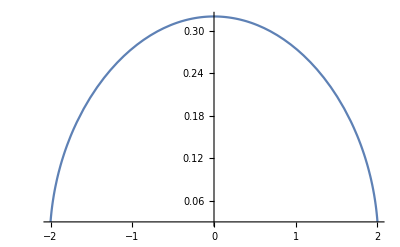

```mathematica
Plot[v[x,.01],{x,-2,2}]
```

```mathematica
TeXForm[(1-(x^2(1-q)q^k)/((1+q^k)^2))]
```

```mathematica
1-\frac{(1-q) x^2 q^k}{(1+q^k)^2}
```

```mathematica
ρ[x_,λ_]:=Piecewise[{{v[x,ⅇ^(-4λ/3)],Abs[x]<2/(√(1-ⅇ^(-4λ/3)))}},0]
```

```mathematica
color[x_]:=Blend[{RGBColor["#3e92cc"],RGBColor["#0a2463"]},x]
```

```mathematica
plot[λ_,sty_,leg_:{}]:=Plot[ρ[x,λ],{x,-2/(√(1-ⅇ^(-4λ/3))),2/(√(1-ⅇ^(-4λ/3)))},PlotRange->{{-3,3},{0,.45}},Frame->False,FrameStyle->Directive[Gray,12],GridLines->Automatic,GridLinesStyle->Directive[Dashed, Gray],Ticks->None,PlotStyle->sty,ImageSize->{800},Background->RGBColor["#edf2f4"],Axes->{False,False},PlotPoints->200,PlotLegends->leg,AspectRatio->.7]
```

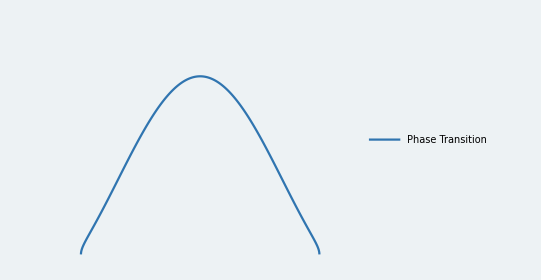

```mathematica
plot[1,color[ⅇ^(-4/3)],Placed[{"Phase Transition"},{Scaled[{.5,0.95}],{.5,0.5}}]]
```

```mathematica
Manipulate[Show[
plot[1/3,color[.2],{}],plot[2/3,color[.4],{}],plot[1,color[.6],{}],plot[5/3,color[.8],{}],
Plot[(√(4-x^2))/(2π),{x,-2,2},PlotStyle->color[1],PlotLegends->Placed[{"Semicircle"},{Scaled[{.3,0.95}],{.5,0.5}}]],
Plot[(ⅇ^(-x^2/2))/(√(2π)),{x,-3,3},PlotStyle->color[0],PlotLegends->Placed[{"Gauss"},{Scaled[{.7,0.95}],{.5,0.5}}]],plot[λ,{RGBColor["#d90429"],Thickness[.003]},Placed[{"Phase Transition"},{Scaled[{.5,0.95}],{.5,0.5}}]]],{λ,.1,3}]
```

```mathematica
dat=Table[Show[
plot[1/3,color[.2],{}],plot[2/3,color[.4],{}],plot[1,color[.6],{}],plot[5/3,color[.8],{}],
Plot[(√(4-x^2))/(2π),{x,-2,2},PlotStyle->color[1],PlotLegends->Placed[{"Semicircle"},{Scaled[{.3,0.95}],{.5,0.5}}]],
Plot[(ⅇ^(-x^2/2))/(√(2π)),{x,-3,3},PlotStyle->color[0],PlotLegends->Placed[{"Gauss"},{Scaled[{.7,0.95}],{.5,0.5}}]],plot[λ,{RGBColor["#d90429"],Thickness[.003]},Placed[{"Phase Transition"},{Scaled[{.5,0.95}],{.5,0.5}}]]],{λ,.1,3,.1}];
```

```mathematica
SetDirectory@NotebookDirectory[]
Export["dos.gif",dat]
```

/Users/dschroeder/Downloads/homepage-cactus/src/content/post/1407.1552

dos.gif

```mathematica
v[1,.5]
```

0.25362